#### Figure 3

```mathematica
sol=ParametricNDSolveValue[{
G'[t]==48-(1.5 E^(-α t) 1/432 B[t] G[t]^2/(G[t]^2+7.85^2) +1.4)G[t],G[0]==5.186146508304312,
B'[t]==B[t] ((1- B[t]/10^5) G[t]/4.8-1),B[0]==7445.730807758443},
{1.5 E^(-α t),G[t]},{t,0,100},{α}];
```

```mathematica
solTopp=ParametricNDSolveValue[{
G'[t]==48-(1.5 E^(-α t) 1/432 B[t] G[t]^2/(G[t]^2+7.85^2) +1.4)G[t],G[0]==4.8,
B'[t]== B[t] ( G[t]/4.8-1),B[0]==9185.875000000002},
{1.5 E^(-α t),G[t]},{t,0,100},{α}];
```

```mathematica
opt2={AspectRatio->1,PlotRange->{{0,1.5},{4,12}},ImageSize->Medium,Frame->True,FrameTicks->{{Range[4,12,1],None},{Range@@{0,1.5,.25},None}},FrameStyle->Directive[Black,"Ariel",14],PlotRangePadding->None,
Prolog->({GrayLevel[.9],Rectangle[{0,4},{1.5,5.7}],GrayLevel[.8],Rectangle[{0,5.7},{1.5,6.9}],Black,Text["Normal",{1.5 .9,4.3}],Text["Prediabetes",{1.5.9,6.3}],Text["Diabetes",{1.5.9,7.2}],
Text["current estimate",Scaled@{.5,.94}],
Text[Style["[",20],Scaled@{.63,.94}]}),
PlotStyle->Thread[{Thick,(ColorData["AvocadoColors"]/@(Rescale@Log@{1/18,1/9,1/3,1/(.9),10/3}))}],PlotLegends->Placed[SwatchLegend[(ColorData["AvocadoColors"]/@(Rescale@Log@{1/18,1/9,1/3,1/(.9),10/3})),{"TiR=6 Tcomp","TiR=3 Tcomp","TiR=1 Tcomp","TiR=0.3 Tcomp","TiR=0.1 Tcomp"}],Scaled@{.8,.85}],FrameLabel->{"Insulin sensetivity (HOMA-IR^-1)","Glucose (mmol/L)"}};
```

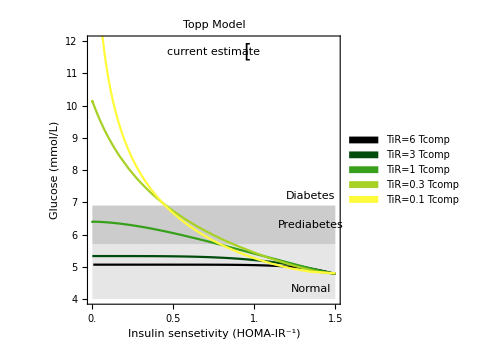
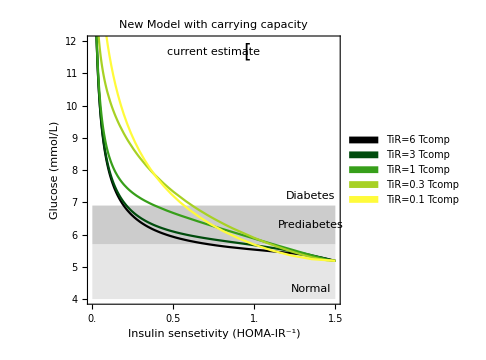

```mathematica
Row[{
ParametricPlot[Evaluate[solTopp/@{1/18,1/9,1/3,1/(.9),10/3}],{t,0,100},Evaluate@opt2,PlotLabel->"Topp Model"],
ParametricPlot[Evaluate[sol/@{1/18,1/9,1/3,1/(.9),10/3}],{t,0,100},Evaluate@opt2,PlotLabel->"New Model with carrying capacity"]},
Spacer@10]//Quiet
```

#### Loading the data and initial processing

[‘Reg.code’,’Date(converted into matlab number)’,’Fasting Glucose (in mmol/L)’,’Fasting Insulin (in micro U/ml)’,’Hba1c (%)’]

```mathematica
Data=Uncompress@;
```

```mathematica
metaData=Dispatch[#[[1]]->Rest@#&/@Uncompress[]];
```

```mathematica
Data1=(*Select[*)
DeleteCases[
({#[[1]],#[[2]],{#[[1]],({G,i,22.5/(i G)(*HOMAs*),(20 i)/(G-3.5)(*HOMAB*),(20i G)/((G-4.8)(G-3.5))(*HOMAC1*),hba1c(*Hba1c (%)*)}/.Thread[{G,i,hba1c}->#[[2;;]]])}&/@#[[3]]}&/@(Join@@(Join@@@Thread[{{StringSplit[FileBaseName[#],"_"][[;;2]]}/.{"female"->"F","male"->"M","Diabetic"->"D","Prediabetic"->"P"},{N@#[[1,1]],#[[;;,2;;]]-Threaded[{#[[1,2]],0,0,0}]}&/@GatherBy[Import[#,"Data"][[2;;]],#[[1]]&]},List,{2}]&/@FileNames["/Users/avimayo/Library/CloudStorage/Box-Box/aurore/segalcohorthba_1cdata/*.txt"]/.metaData))),
{_,_,{___,{_,{___,_?(#<0&),___}},___}},∞];
```

```mathematica
MData=({#[[1]],#[[2]],(*MeanAround*)If[Length@#>1,Around[Mean@#,StandardDeviation@#],#[[1]]]&/@(#[[3,;;,2]]ᵀ)}&/@Data1);
```

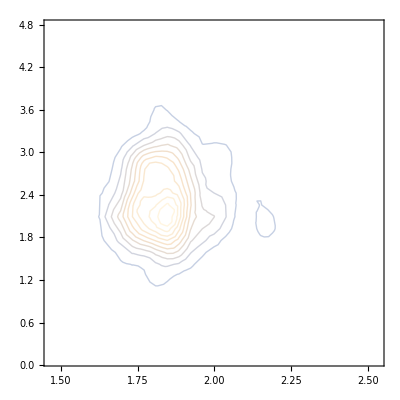

```mathematica
SmoothDensityHistogram[Log[MData[[;;,3,;;2]]/.Around[x_,y_]:>x],Mesh->10,MeshShading->{None,None},PlotRange->All]
```

```mathematica
(pts=Cases[#,{{_Real,_Real}..},∞][[1]];Rs=RegionMember@BoundaryMeshRegion[pts,#]&/@Cases[#,Line[x_,_]:>Line[x],∞])&@SmoothDensityHistogram[Log[MData[[;;,3,;;2]]/.Around[x_,y_]:>x],Mesh->100,MeshShading->{None,None},PlotRange->All];
R=TakeWhile[ReverseSortBy[Table[{r,N@((Length@Select[#,r])/(Length@#))&@(Log[MData[[;;,3,;;2]]/.Around[x_,y_]:>x])},{r,Rs}],Last],#[[2]]>.95&][[-1,1]]
```

RegionMemberFunction[BoundaryMeshRegion[<2>, <2>], <>]

```mathematica
MData95=Select[
Select[
MData,
R[Log[#[[3,;;2]]/.Around[x_,y_]:>x]]&],
(#[[3,1]]/.Around[x_,_]:>x)>5.6&];
```

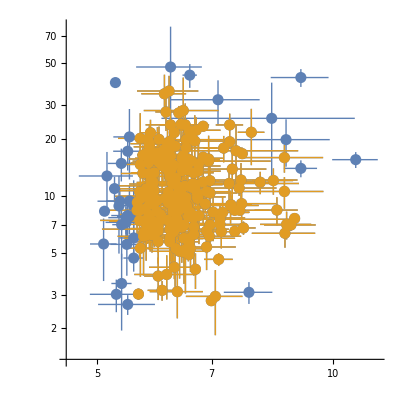

```mathematica
ListLogLogPlot[
Evaluate[{
MData[[;;,3,;;2]],
MData95[[;;,3,;;2]]}],PlotRange->All,AspectRatio->1,PlotStyle->PointSize[.02]]
```

#### All combinations of 2 parameter sets

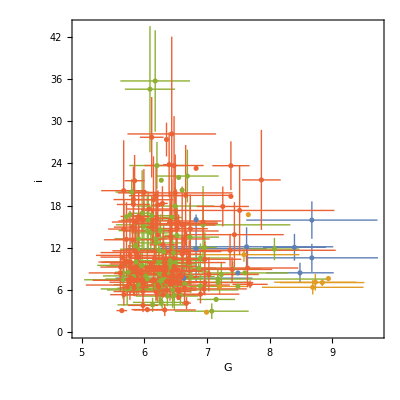
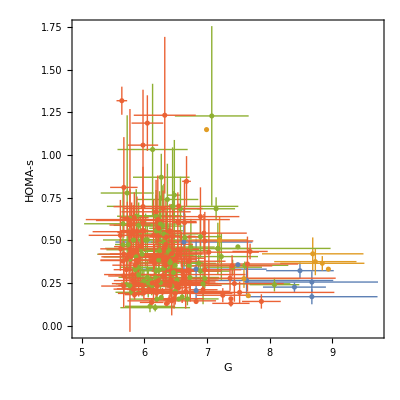
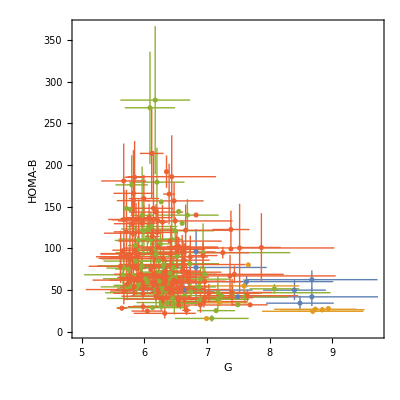
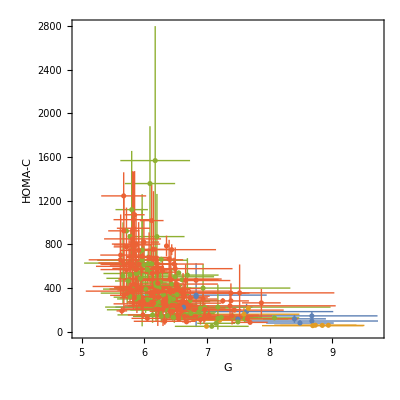
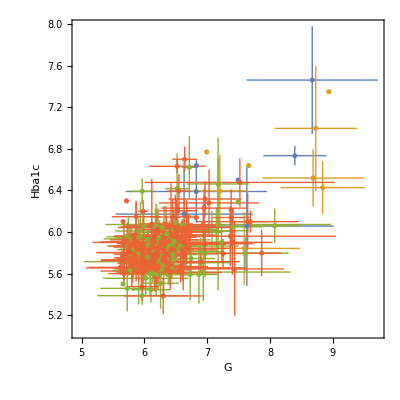
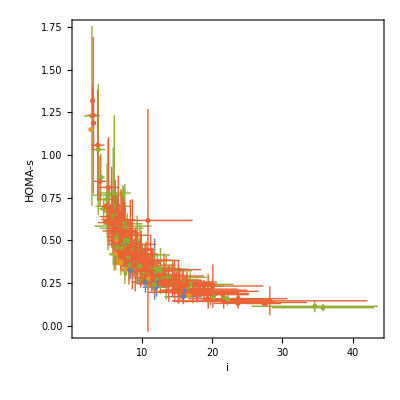
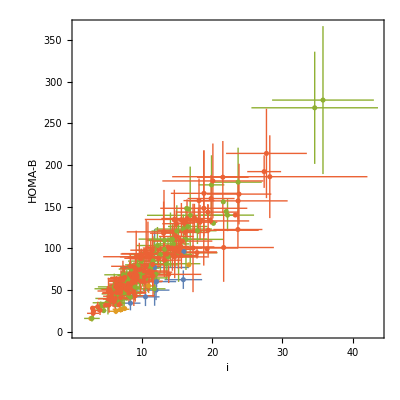
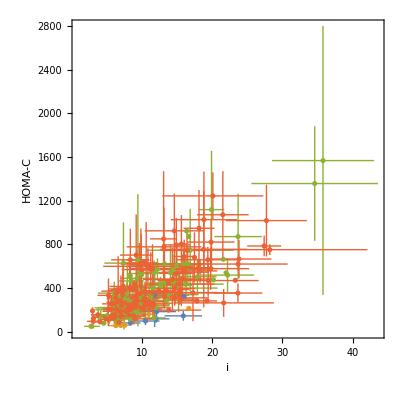
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- |  |  | 
-Graphics- |  |  |  |

```mathematica
Grid@TakeList[ListPlot[GatherBy[MData95,#[[1]]&][[;;,;;,3,#]](*,ScalingFunctions->{"Log10","Log10"}*),AspectRatio->1,Frame->True,PlotRange->All,FrameLabel->{"G","i","HOMA-s","HOMA-B","HOMA-C","Hba1c"}[[#]]]&/@Subsets[Range@6,{2}],Reverse@Range@5]
```

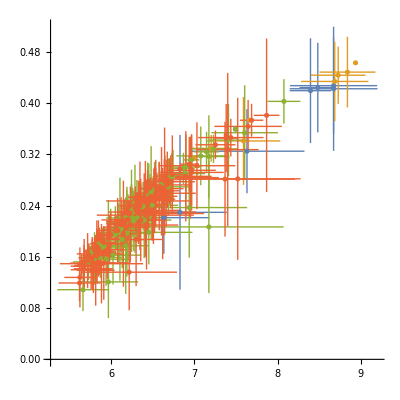

```mathematica
ListPlot[Map[{#[[1]],(#[[2]])/(#[[3]])}&,GatherBy[MData95,#[[1]]&][[;;,;;,3,{1,4,5}]],{2}],PlotRange->All,AspectRatio->1]
```

#### All parameters vs. age and BMI

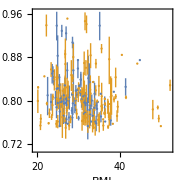
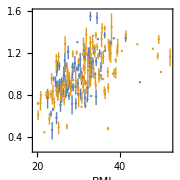
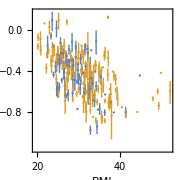
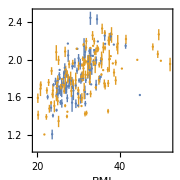
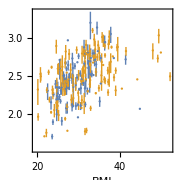
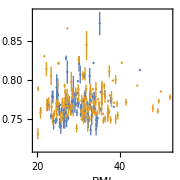

```mathematica
Row[Table[ListPlot[
GatherBy[{#[[1,2]],#[[2,3]],#[[3,i]]}&/@Cases[MData95,{{_,_},{__},__}],First][[;;,;;,2;;]],PlotRange->All,ImageSize->Small,ScalingFunctions->{Automatic,"Log10"},AspectRatio->1,Frame->True,FrameLabel->{"BMI",{"G","i","HOMA-s","HOMA-B","HOMA-C","Hba1c"}[[i]]}],{i,Range@6}],Spacer@10]
```

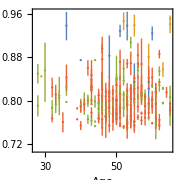
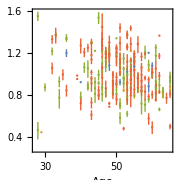
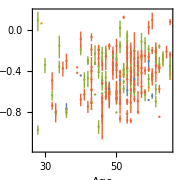
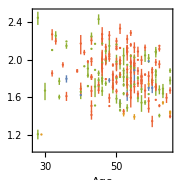
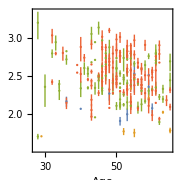
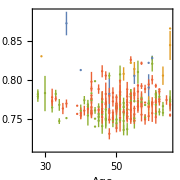

```mathematica
Row[Table[ListPlot[
GatherBy[{#[[1]],#[[2,2]],#[[3,i]]}&/@Cases[MData95,{{_,_},{__},__}],First][[;;,;;,2;;]],PlotRange->All,ImageSize->Small,ScalingFunctions->{Automatic,"Log10"},AspectRatio->1,Frame->True,FrameStyle->Directive["Ariel",14],FrameTicks->{{Automatic,None},{Range@@{30,60,10},None}},FrameLabel->{"Age",{"G","i","HOMA-s","HOMA-B","HOMA-C","Hba1c"}[[i]]}],{i,Range@6}],Spacer@10]
```

#### Figure 4 - First time point only

```mathematica
MData95FTP={#[[1]],#[[2]],#[[3,1,2]]}&/@Select[Data1,MemberQ[MData95[[;;,;;2]],#[[;;2]]]&];
```

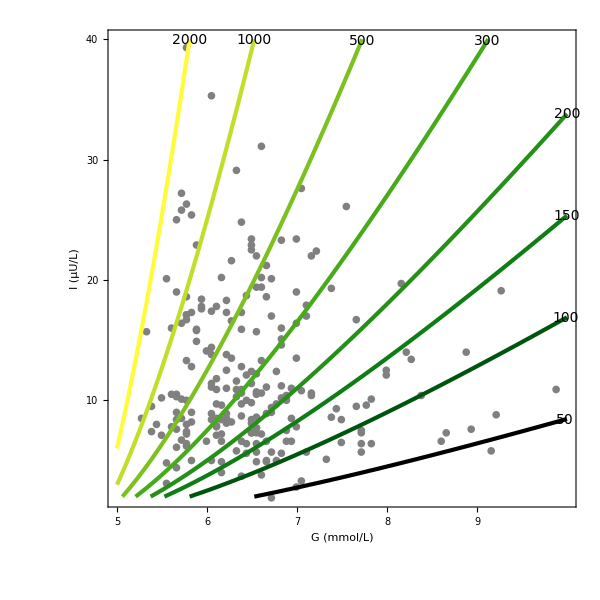
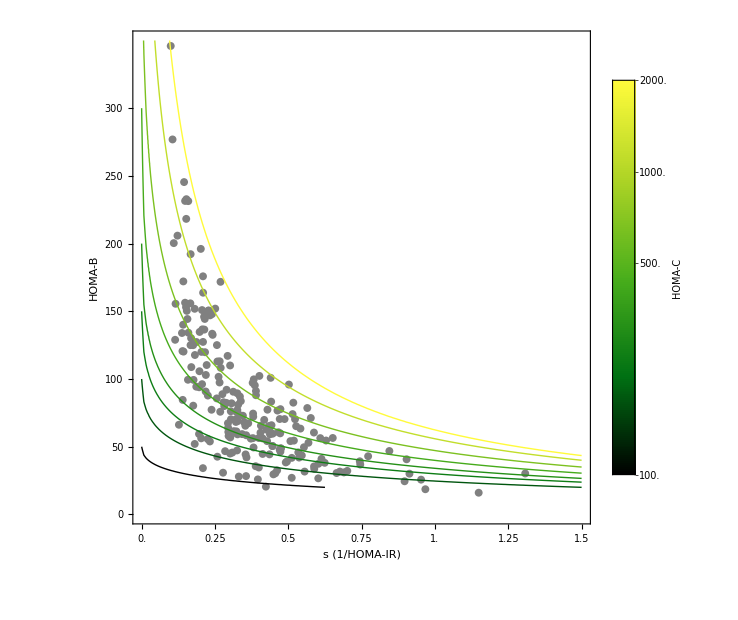
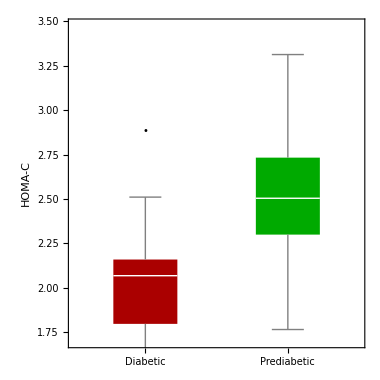
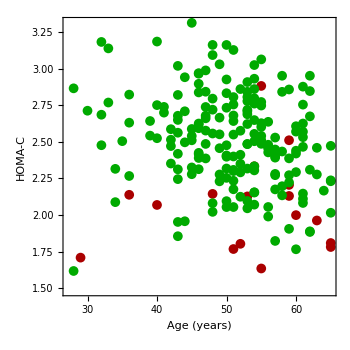
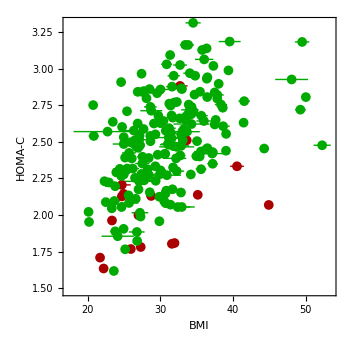
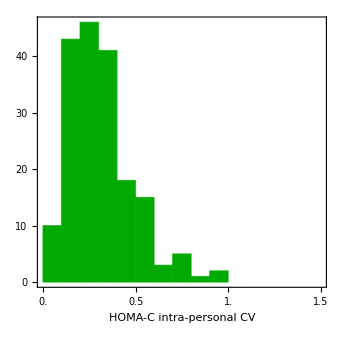

```mathematica
Column[
{Row[{
Show[{
ListPlot[MData95FTP[[;;,3,{1,2}]],PlotStyle->{GrayLevel[.5]}],

ContourPlot[(20i G)/((G-4.8)(G-3.5)),{G,5,10},{i,2,40},ScalingFunctions->"Log10",ContourShading->None,Contours->Log10@{50,100,150,200,300,500,1000,2000},ContourStyle->Thread[{Thickness[.005],(ColorData["AvocadoColors"]/@N@Rescale@Log10@{50,100,150,200,300,500,1000,2000})}],ContourLabels->(Text[Style[10^#3,{"Ariel",Black,14}],{#1,#2},Background->White]&),PlotPoints->50]},

Frame->True,Axes->False,PlotRange->All,AspectRatio->1,PlotRangePadding->Scaled@.025,FrameLabel->{"G (mmol/L)","I (μU/L)"},ImageSize->600,FrameTicks->{{Range[10,40,10],None},{Range[5,9],None}},FrameStyle->Directive[Black,"Ariel",20]],
Legended[
Show[{
ListPlot[MData95FTP[[;;,3,{3,4}]],PlotStyle->{GrayLevel[.5]},PlotRange->{{0,1.5},{0,350}}],
ContourPlot[(5. (-375. HOMAB-7. HOMAB^2 HOMAs-1. √(7200. HOMAB^3 HOMAs+49. HOMAB^4 HOMAs^2)))/(-1875.+26. HOMAB HOMAs),{HOMAs,0,1.5},{HOMAB,20,350},
Contours->Log10@{50,100,150,200,300,500,1000,2000},ScalingFunctions->"Log10",ContourShading->None,ContourStyle->Thread[{Thick,(ColorData["AvocadoColors"]/@N@Rescale@Log10@{50,100,150,200,300,500,1000,2000})}],Exclusions->None,PlotPoints->50]
},
Frame->True,Axes->False,AspectRatio->1,PlotRangePadding->None,FrameLabel->{"s (1/HOMA-IR)","HOMA-B"},ImageSize->620,FrameTicks->{{Range[0,300,50],None},{Range[0,1.5,.25],None}},FrameStyle->Directive[Black,"Ariel",20],PlotRange->{{0,1.5},{0,350}}],Placed[BarLegend["AvocadoColors","Ticks"->N@Rescale@Log10@{100,500,1000,2000},"TickLabels"->(Style[#,Directive["Ariel",14]]&/@{100,500,1000,2000}),LegendLabel->Style["HOMA-C",Directive[Black,"Ariel",20]]],Scaled@{.85,.65}]]},
Spacer@50],
Row[{
BoxWhiskerChart[#,"Outliers",ChartLabels->{"Diabetic","Prediabetic"},ChartStyle->Darker@{Red,Green},PlotRange->{{0.5,2.5},Log10@{50,3 10^3}},Sequence[ScalingFunctions->"Log10",ImageSize->380,FrameLabel->{None,"HOMA-C"},AspectRatio->1,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,"Ariel",20]]]&@((GatherBy[MData95FTP,#[[1,1]]&][[;;,;;,3,5]])),

ListPlot[
{#[[;;,2,2]],#[[;;,3,5]]}ᵀ&/@GatherBy[Cases[MData95FTP,{{_,_},{__},__}],#[[1,1]]&],
PlotRange->All,ImageSize->350,ScalingFunctions->{Automatic,"Log10"},AspectRatio->1,Frame->True,FrameTicks->{{Automatic,None},{Range@@{30,60,10},None}},FrameStyle->Directive["Ariel",Black,20],PlotStyle->Thread[{PointSize[.02],Darker@{Red,Green}}],FrameLabel->{"Age (years)","HOMA-C"}],

ListPlot[
{Around@@@#[[;;,2,3;;]],#[[;;,3,5]]}ᵀ&/@GatherBy[Cases[MData95FTP,{{_,_},{__},__}],#[[1,1]]&],PlotRange->All,ImageSize->350,ScalingFunctions->{Automatic,"Log10"},AspectRatio->1,Frame->True,FrameLabel->{"BMI","HOMA-C"},FrameTicks->{{Automatic,None},{Range@@{20,50,10},None}},FrameStyle->Directive["Ariel",20,Black],PlotStyle->Thread[{PointSize[.02],Darker@{Red,Green}}]],

Histogram[(StandardDeviation@#)/(Mean@#)&/@Select[#,Length@#>1&],
Axes->True,AxesOrigin->{(StandardDeviation@#)/(Mean@#)&@Flatten@#,0},PlotRange->{{0,1.5},All},Frame->True,ImageSize->340,FrameLabel->{"HOMA-C intra-personal CV",""},ChartStyle->Darker@Green,FrameStyle->Directive[Black,"Ariel",20],AspectRatio->1,FrameTicks->{{Range@@{0,50,10},None},{Range@@{0,1.5,.5},None}},Epilog->Rotate[Text[Style["HOMA-C inter-personal CV","Ariel",14,Black],Scaled@{.5,.5}],π/2]]&@GatherBy[Select[Data1,MemberQ[MData95[[;;,;;2]],#[[;;2]]]&],#[[1,1]]&][[2,;;,3,;;,2,5]]},

Spacer@10]},
Alignment->Center,Spacings->2]
```

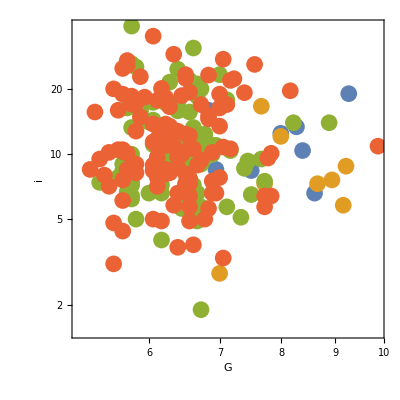
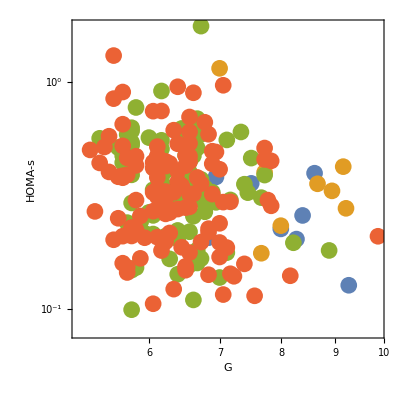
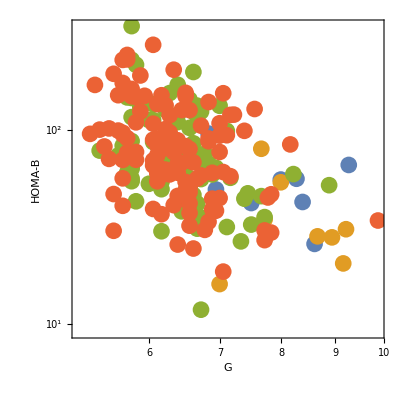
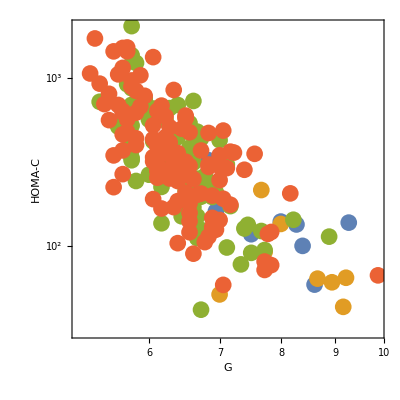
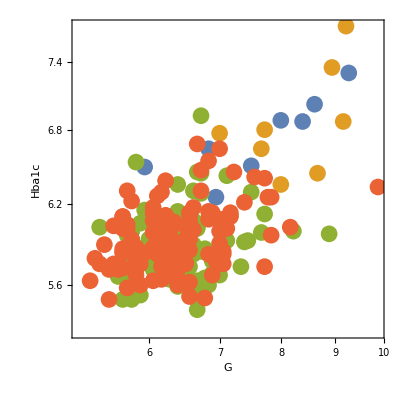
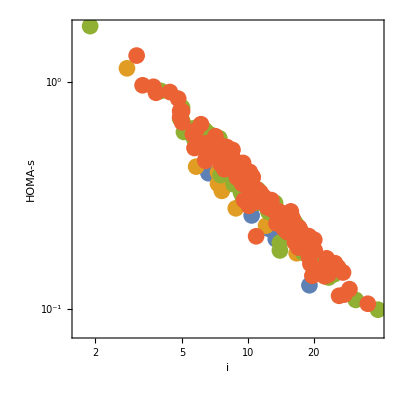
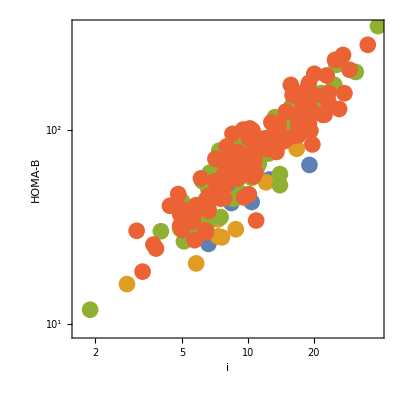
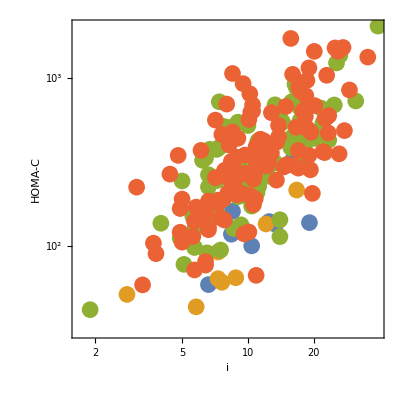
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- |  |  | 
-Graphics- |  |  |  |

```mathematica
Grid@TakeList[ListPlot[GatherBy[MData95FTP,#[[1]]&][[;;,;;,3,#]],ScalingFunctions->{"Log10","Log10"},AspectRatio->1,Frame->True,PlotRange->All,FrameLabel->{"G","i","HOMA-s","HOMA-B","HOMA-C","Hba1c"}[[#]],PlotStyle->PointSize[.03]]&/@Subsets[Range@6,{2}],Reverse@Range@5]
```

#### Figure S4 - all time points

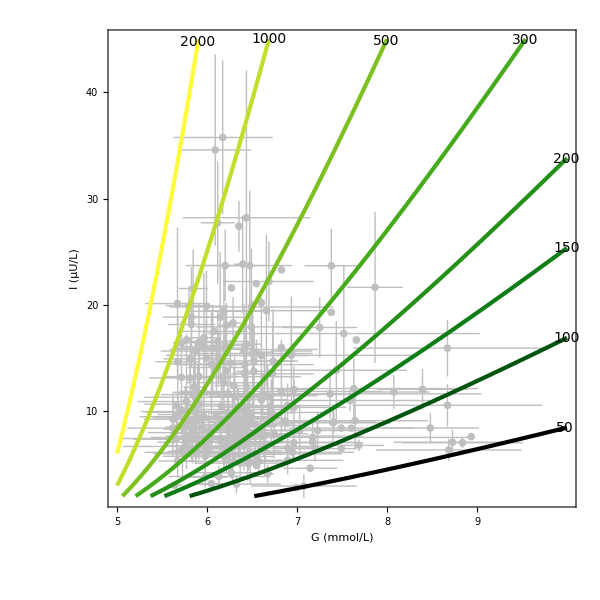
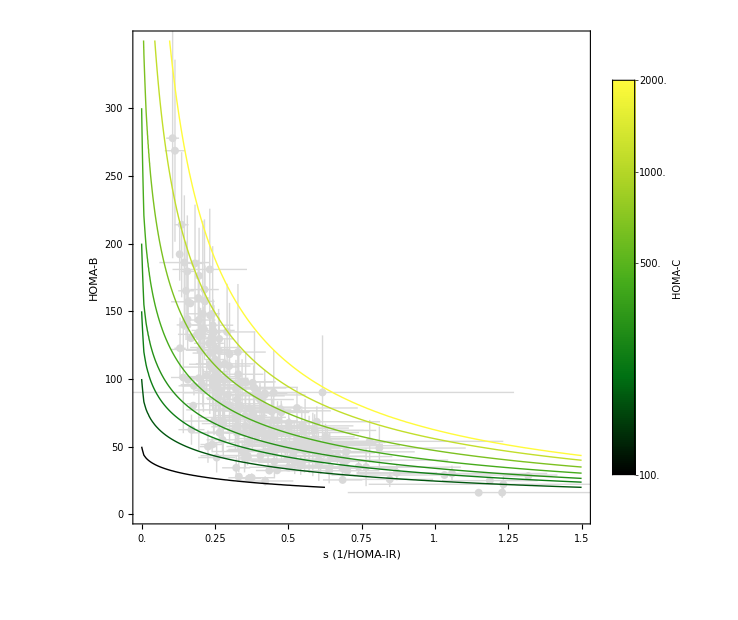
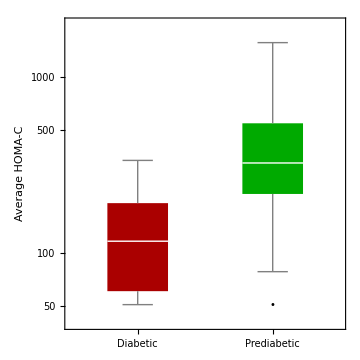
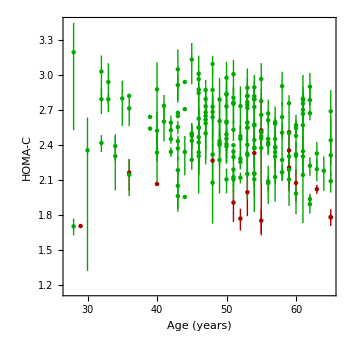
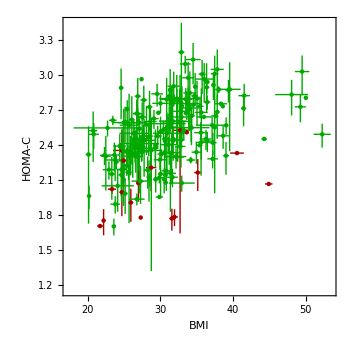
-Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Column[
{Row[{
Show[{
ListPlot[MData95[[;;,3,{1,2}]],PlotStyle->{GrayLevel[.75]}],

ContourPlot[(20i G)/((G-4.8)(G-3.5)),{G,5,10},{i,2,45},ScalingFunctions->"Log10",ContourShading->None,Contours->Log10@{50,100,150,200,300,500,1000,2000},ContourStyle->Thread[{Thickness[.005],(ColorData["AvocadoColors"]/@N@Rescale@Log10@{50,100,150,200,300,500,1000,2000})}],ContourLabels->(Text[Style[10^#3,{"Ariel",Black,14}],{#1,#2},Background->White]&),PlotPoints->50]},

Frame->True,Axes->False,PlotRange->All,AspectRatio->1,PlotRangePadding->Scaled@.025,FrameLabel->{"G (mmol/L)","I (μU/L)"},ImageSize->600,FrameTicks->{{Range[10,40,10],None},{Range[5,9],None}},FrameStyle->Directive[Black,"Ariel",20]],
Legended[
Show[{
ListPlot[MData95[[;;,3,{3,4}]],PlotStyle->{GrayLevel[.85]},PlotRange->{{0,1.5},{0,350}}],
ContourPlot[(5. (-375. HOMAB-7. HOMAB^2 HOMAs-1. √(7200. HOMAB^3 HOMAs+49. HOMAB^4 HOMAs^2)))/(-1875.+26. HOMAB HOMAs),{HOMAs,0,1.5},{HOMAB,20,350},
Contours->Log10@{50,100,150,200,300,500,1000,2000},ScalingFunctions->"Log10",ContourShading->None,ContourStyle->Thread[{Thick,(ColorData["AvocadoColors"]/@N@Rescale@Log10@{50,100,150,200,300,500,1000,2000})}],Exclusions->None,PlotPoints->50]
},
Frame->True,Axes->False,AspectRatio->1,PlotRangePadding->None,FrameLabel->{"s (1/HOMA-IR)","HOMA-B"},ImageSize->620,FrameTicks->{{Range[0,300,50],None},{Range[0,1.5,.25],None}},FrameStyle->Directive[Black,"Ariel",20],PlotRange->{{0,1.5},{0,350}}],Placed[BarLegend["AvocadoColors","Ticks"->N@Rescale@Log10@{100,500,1000,2000},"TickLabels"->(Style[#,Directive["Ariel",14]]&/@{100,500,1000,2000}),LegendLabel->Style["HOMA-C",Directive[Black,"Ariel",20]]],Scaled@{.85,.65}]]},
Spacer@50],
Row[{

BoxWhiskerChart[Log10@#,"Outliers",ChartLabels->{"Diabetic","Prediabetic"},ChartStyle->Darker@{Red,Green},PlotRange->{{0.5,2.5},Log10@{40,2 10^3}},ImageSize->Medium,FrameLabel->{None,"Average HOMA-C"},AspectRatio->1,FrameTicks->{{{Log10[#],#}&/@{50,100,500,1000},None},{Automatic,None}},FrameStyle->Directive[Black,"Ariel",14]]&@((GatherBy[MData95,#[[1,1]]&][[;;,;;,3,5]]/.Around[x_,y_]:>x)),

ListPlot[
{#[[;;,2,2]],#[[;;,3,5]]}ᵀ&/@GatherBy[Cases[MData95,{{_,_},{__},__}],#[[1,1]]&],
PlotRange->All,ImageSize->350,ScalingFunctions->{Automatic,"Log10"},AspectRatio->1,Frame->True,FrameTicks->{{Automatic,None},{Range@@{30,60,10},None}},FrameStyle->Directive["Ariel",Black,20],PlotStyle->Darker@{Red,Green},FrameLabel->{"Age (years)","HOMA-C"}],

ListPlot[
{Around@@@#[[;;,2,3;;]],#[[;;,3,5]]}ᵀ&/@GatherBy[Cases[MData95,{{_,_},{__},__}],#[[1,1]]&],PlotRange->All,ImageSize->350,ScalingFunctions->{Automatic,"Log10"},AspectRatio->1,Frame->True,FrameLabel->{"BMI","HOMA-C"},FrameTicks->{{Automatic,None},{Range@@{20,50,10},None}},FrameStyle->Directive["Ariel",20,Black],PlotStyle->Darker@{Red,Green}],


Histogram[(StandardDeviation@#)/(Mean@#)&/@Select[#,Length@#>1&],
Axes->True,AxesOrigin->{(StandardDeviation@#)/(Mean@#)&@Flatten@#,0},PlotRange->{{0,1.5},All},Frame->True,ImageSize->340,FrameLabel->{"HOMA-C intra-personal CV",""},ChartStyle->Darker@Green,FrameStyle->Directive[Black,"Ariel",20],AspectRatio->1,FrameTicks->{{Range@@{0,50,10},None},{Range@@{0,1.5,.5},None}},Epilog->Rotate[Text[Style["HOMA-C inter-personal CV","Ariel",14,Black],Scaled@{.5,.5}],π/2]]&@GatherBy[Select[Data1,MemberQ[MData95[[;;,;;2]],#[[;;2]]]&],#[[1,1]]&][[2,;;,3,;;,2,5]]},

Spacer@10]},
Alignment->Center,Spacings->2]
```